```mathematica
βm[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m+1)/2}]]->-t]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]= ReplacePart[βm[ω,δ,t,ϵ,m],{{m,m+1},{m+1,m}}->0]
```

```mathematica
T1[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m+1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m+1)/2}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T:=T1[1,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T].J.T].B,6000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=T1[1,m]},
sl1= Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,2m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[T].J.T].c],4]; J=J]; Il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,1,0,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
Timing[tr[1,0.0001,1,0,0,4]]
```

{0.008233,1.97669}

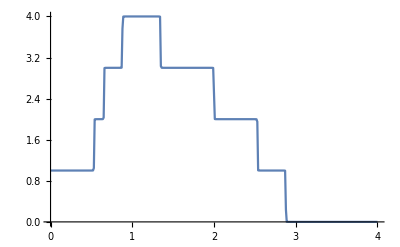

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.001,1,0,0,8]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Δ[ω_,m_,N_]:=Δ[ω,m,N]=Abs[Mean[Table[tr[ω,0.001,1,0,1,m],N+100]]-Mean[Table[tr[ω,0.001,1,0,1,m],N]]]
```

```mathematica
Table[{N,Δ[1,8,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0168211},{2500,0.033501},{3000,0.00879139},{3500,0.00652042},{4000,0.0100108},{4500,0.0110463},{5000,0.00110255},{5500,0.0129938},{6000,0.0148439},{6500,0.00534785},{7000,0.0107431},{7500,0.00968844},{8000,0.00200109},{8500,0.00515762},{9000,0.00102956},{9500,0.00557833},{10000,0.0044145}}

```mathematica
Table[{N,Δ[1,10,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0241843},{2500,0.0316241},{3000,0.0064626},{3500,0.0111572},{4000,0.000889049},{4500,0.00390552},{5000,0.00186596},{5500,0.00216894},{6000,0.0162093},{6500,0.00342894},{7000,0.0211225},{7500,0.00514544},{8000,0.0072816},{8500,0.00601826},{9000,0.000185366},{9500,0.00519082},{10000,0.00671868}}

```mathematica
Table[{N,Δ[1,12,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0289622},{2500,0.0221254},{3000,0.000778363},{3500,0.0173281},{4000,0.00782032},{4500,0.0168419},{5000,0.0159904},{5500,0.0198165},{6000,0.0222215},{6500,0.0299706},{7000,0.00834148},{7500,0.00687671},{8000,0.0327704},{8500,0.00118289},{9000,0.00232364},{9500,0.000269632},{10000,0.0147986}}

```mathematica
Table[{N,Δ[1,14,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0219257},{2500,0.0360234},{3000,0.00430806},{3500,0.0118009},{4000,0.0253681},{4500,0.0110953},{5000,0.0474155},{5500,0.00427758},{6000,0.00718471},{6500,0.00791052},{7000,0.0117195},{7500,0.000533116},{8000,0.0219269},{8500,0.0121023},{9000,0.00788726},{9500,0.00556168},{10000,0.00304123}}

```mathematica
Table[{N,Δ[1,16,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0958251},{2500,0.0177262},{3000,0.0215497},{3500,0.0474833},{4000,0.00628304},{4500,0.00152025},{5000,0.0132051},{5500,0.0442877},{6000,0.0479593},{6500,0.00104508},{7000,0.00269678},{7500,0.0137058},{8000,0.0487861},{8500,0.00813944},{9000,0.00634451},{9500,0.00162871},{10000,0.00860073}}

```mathematica
Table[{N,Δ[1,18,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.00560597},{2500,0.0161467},{3000,0.0848936},{3500,0.020609},{4000,0.00562626},{4500,0.00753007},{5000,0.0309255},{5500,0.0232819},{6000,0.0670423},{6500,0.00858689},{7000,0.0466227},{7500,0.0168067},{8000,0.00806501},{8500,0.0287003},{9000,0.0021114},{9500,0.0142346},{10000,0.0191757}}

```mathematica
Table[{N,Δ[1,6,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.0125396},{2500,0.00457259},{3000,0.0115563},{3500,0.0063896},{4000,0.00928293},{4500,0.00568621},{5000,0.00479712},{5500,0.00400197},{6000,0.00833561},{6500,0.000345568},{7000,0.00322255},{7500,0.0134724},{8000,0.00651145},{8500,0.00531597},{9000,0.0106456},{9500,0.000469253},{10000,0.000225674}}

```mathematica
Table[{N,Δ[1,4,N]},{N,Range[2000,10000,500]}]
```

{{2000,0.00183837},{2500,0.0071935},{3000,0.000907917},{3500,0.0106837},{4000,0.0161582},{4500,0.0148967},{5000,0.00257023},{5500,0.00263956},{6000,0.00389152},{6500,0.00678209},{7000,0.00132818},{7500,0.0022759},{8000,0.00784911},{8500,0.00827783},{9000,0.00468013},{9500,0.00133367},{10000,0.00255332}}

```mathematica
Min[%190]
```

0.0021114

```mathematica
{{4,3000},{6,10000},{8,9000},{10,4000},{12,2700},{14,3000},{16,4000},{18,4000}}
```

```mathematica
Δ[1,8,100000]
```

$Aborted

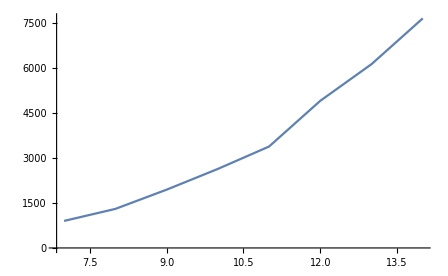

```mathematica
ListLinePlot[{{7,900},{8,1300},{9,1940},{10,2631},{11,3377},{12,4900},{13,6121},{14,7645}}]
```

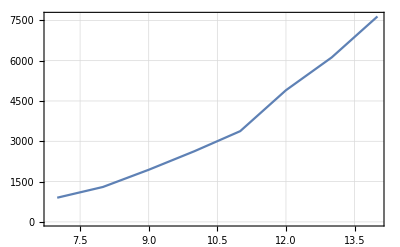

```mathematica
ListLinePlot[{{7,900},{8,1300},{9,1940},{10,2631},{11,3377},{12,4900},{13,6121},{14,7645}},PlotTheme->"Detailed"]
```

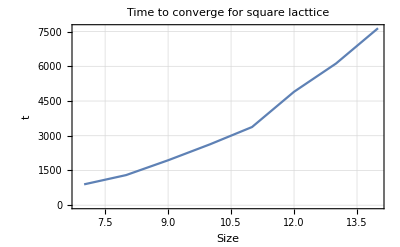

```mathematica
Show[%58,FrameLabel->{{HoldForm[t],None},{HoldForm[Size],None}},PlotLabel->HoldForm[Time to converge for square lacttice],LabelStyle->{GrayLevel[0]}]
```